# Trave appoggio-appoggio elastico

```mathematica
ClearAll["Global`*"]

v[s_] = c1+c2*s+c3*Cos[α*s]+c4*Sin[α*s];

{RR, MM} = CoefficientArrays[
{
v[0] == 0,
v''[0]==0,
v''[l]==0,
-l^3/β*(v'''[l]+α^2*v'[l])==-v[l]
},
{c1,c2,c3,c4}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | 0 | -α^2 | 0
0 | 0 | -α^2 Cos[l α] | -α^2 Sin[l α]
1 | l-(l^3 α^2)/β | Cos[l α] | Sin[l α])

(0
0
0
0)

```mathematica
Clear[detMM, α, β, l]
detMM[α_] = Det[MM]//Simplify

Solve[(-l^2 α^2+β)==0, α]
Solve[Sin[l α]==0, α]
```

(l α^4 (-l^2 α^2+β) Sin[l α])/β

{{α→-(√β)/l},{α→(√β)/l}}

{{α→ConditionalExpression[(2 π C[1])/l, C[1]∈ℤ]},{α→ConditionalExpression[(π+2 π C[1])/l, C[1]∈ℤ]}}

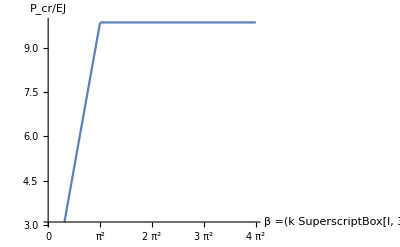

```mathematica
Plot[{If[β<= Pi^2, β,Pi^2]}, {β, 0,4*Pi^2}, AxesLabel->{"β =(k SuperscriptBox[l, 3])/EJ", "P_cr/EJ"}, Ticks->{Table[k*Pi^2, {k, 0, 4}], Automatic}]
```

## β -> 0 (k->0)

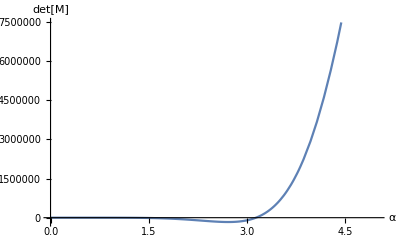

```mathematica
ClearAll[α, αcr, MMcr, β, l]
β=.001;
l=1;
Plot[detMM[α], {α, 0, 5}, AxesLabel->{"α", "det[M]"}]
```

```mathematica
αcr = α/.FindRoot[detMM[α]==0, {α, 4}]
Pi//N
```

3.14159

3.14159

```mathematica
MMcr = MM/.α->αcr//Chop;
MatrixForm[MMcr]
Eigensystem[MMcr]
{c1, c2, c3, c4}=Eigenvectors[MMcr][[-2]]
```

(1 | 0 | 1 | 0
0 | 0 | -9.8696 | 0
0 | 0 | 9.8696 | 0
1 | -985.96 | -1. | 0)

{{9.8696,1.,0.,0.},{{0.00112949,-0.0100181,0.0100181,0.999899},{0.707107,0.,0.,0.707107},{0.,0.,0.,1.},{0.,0.,0.,0.}}}

{0.,0.,0.,1.}

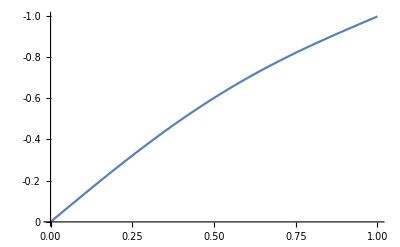

```mathematica
Plot[v[s]/.α->αcr,{s, 0, l}, ScalingFunctions->"Reverse"]
```

## β = kl^3/EJ = 10

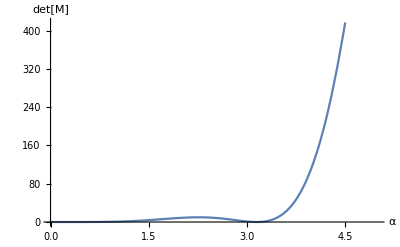

```mathematica
ClearAll[α, αcr, MMcr, β, l]
β=10;
l=1;
Plot[detMM[α], {α, 0, 5}, AxesLabel->{"α", "det[M]"}]
```

```mathematica
αcr = α/.FindRoot[detMM[α]==0, {α, 4}]
Pi//N
```

3.16228

3.14159

```mathematica
MMcr = MM/.α->αcr//Chop;
MatrixForm[MMcr]
Eigensystem[MMcr]
{c1, c2, c3, c4}=Eigenvectors[MMcr][[-1]]
```

(1 | 0 | 1 | 0
0 | 0 | -10. | 0
0 | 0 | 9.99786 | 0.206835
1 | 0 | -0.999786 | -0.0206835)

{{9.97949,0.976466,0.0212256,0.},{{-0.0782707,0.704275,-0.702831,0.0624399},{0.688062,0.165829,-0.0161927,0.706264},{-0.0021573,-0.994795,0.00211151,-0.101848},{0.,1.,0.,0.}}}

{0.,1.,0.,0.}

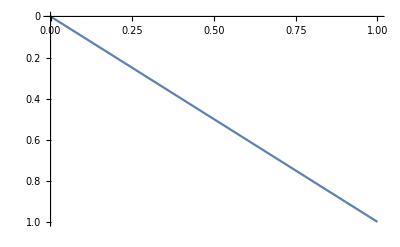

```mathematica
Plot[v[s]/.α->αcr,{s, 0, l}, ScalingFunctions->"Reverse"]
```

```mathematica
ClearAll["Global`*"]

v[s_] = c1+c2*s+c3*Cos[α*s]+c4*Sin[α*s];

{RR, MM} = CoefficientArrays[
{
v[0] == 0,
v'[0]==0,
v''[l]==0,
-l^3/β*(v'''[l]+α^2*v'[l])==-v[l]
},
{c1,c2,c3,c4}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | α
0 | 0 | -α^2 Cos[l α] | -α^2 Sin[l α]
1 | l-(l^3 α^2)/β | Cos[l α] | Sin[l α])

(0
0
0
0)

```mathematica
Clear[detMM]
detMM[α_] = Det[MM]//Simplify
```

-(α^2 (l α (l^2 α^2-β) Cos[l α]+β Sin[l α]))/β

100000

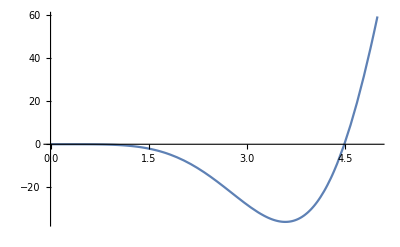

```mathematica
β=100000
l=1;
Plot[detMM[α], {α, 0, 5}]
```

```mathematica
FindRoot[detMM[α]==0,{α,4}]
```

{α→4.49336}

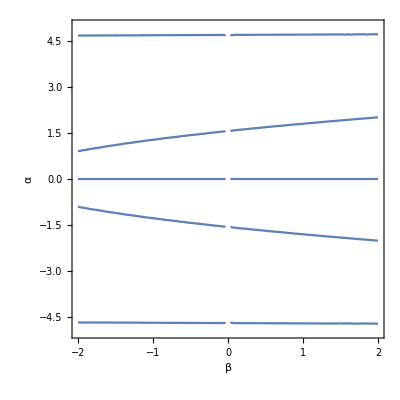

```mathematica
β=.;
α=.;
l=1;
ContourPlot[{detMM[α]==0}, {β, -2, 2},  {α, -5, 5}, Mesh->None, FrameLabel->{"β", "α"}]
```

## β = kl^3/EJ = 15

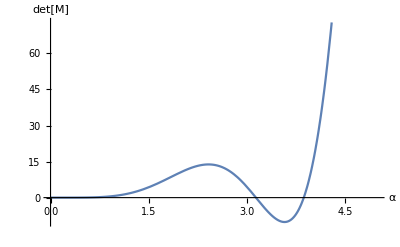

```mathematica
ClearAll[α, αcr, MMcr, β, l]
β=15;
l=1;
Plot[detMM[α], {α, 0, 5}, AxesLabel->{"α", "det[M]"}]
```

```mathematica
αcr = α/.FindRoot[detMM[α]==0, {α, 4}]
Pi//N
```

3.87298

3.14159

```mathematica
MMcr = MM/.α->αcr//Chop;
MatrixForm[MMcr]
Eigensystem[MMcr]
{c1, c2, c3, c4}=Eigenvectors[MMcr][[-1]]
```

(1 | 0 | 1 | 0
0 | 0 | -15. | 0
0 | 0 | 11.1637 | 10.0186
1 | 0 | -0.744246 | -0.667905)

{{10.5944,0.450718+0.861688 ⅈ,0.450718-0.861688 ⅈ,0.},{{-0.0599892+0. ⅈ,0.814902+0. ⅈ,-0.575557+0. ⅈ,0.0327081+0. ⅈ},{0.0313941-0.0546575 ⅈ,-0.993531+0. ⅈ,0.0298535+0.0570742 ⅈ,-0.0368316-0.0584624 ⅈ},{0.0313941+0.0546575 ⅈ,-0.993531+0. ⅈ,0.0298535-0.0570742 ⅈ,-0.0368316+0.0584624 ⅈ},{0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}}

{0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Plot[v[s]/.α->αcr,{s, 0, l}, ScalingFunctions->"Reverse"]
```

-Graphics-

```mathematica
ClearAll["Global`*"]

v[s_] = c1+c2*s+c3*Cos[α*s]+c4*Sin[α*s];

{RR, MM} = CoefficientArrays[
{
v[0] == 0,
v'[0]==0,
v''[l]==0,
-l^3/β*(v'''[l]+α^2*v'[l])==-v[l]
},
{c1,c2,c3,c4}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | α
0 | 0 | -α^2 Cos[l α] | -α^2 Sin[l α]
1 | l-(l^3 α^2)/β | Cos[l α] | Sin[l α])

(0
0
0
0)

```mathematica
Clear[detMM]
detMM[α_] = Det[MM]//Simplify
```

-(α^2 (l α (l^2 α^2-β) Cos[l α]+β Sin[l α]))/β

```mathematica
β=100000
l=1;
Plot[detMM[α], {α, 0, 5}]
```

100000

-Graphics-

```mathematica
FindRoot[detMM[α]==0,{α,4}]
```

{α→4.49336}

```mathematica
β=.;
α=.;
l=1;
ContourPlot[{detMM[α]==0}, {β, -2, 2},  {α, -5, 5}, Mesh->None, FrameLabel->{"β", "α"}]
```

-Graphics-

## β = kl^3/EJ = 10000

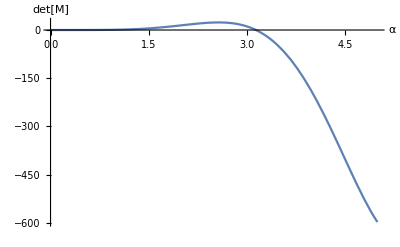

```mathematica
ClearAll[α, αcr, MMcr, β, l]
β=10000;
l=1;
Plot[detMM[α], {α, 0, 5}, AxesLabel->{"α", "det[M]"}]
```

```mathematica
αcr = α/.FindRoot[detMM[α]==0, {α, 4}]
Pi//N
```

3.14159

3.14159

```mathematica
MMcr = MM/.α->αcr//Chop;
MatrixForm[MMcr]
Eigensystem[MMcr]
{c1, c2, c3, c4}=Eigenvectors[MMcr][[-2]]
```

(1 | 0 | 1 | 0
0 | 0 | -9.8696 | 0
0 | 0 | 9.8696 | 0
1 | 0.999013 | -1. | 0)

{{9.8696,1.,0.,0.},{{0.0787589,-0.69856,0.69856,-0.133508},{0.707107,0.,0.,0.707107},{0.,0.,0.,1.},{0.,0.,0.,0.}}}

{0.,0.,0.,1.}

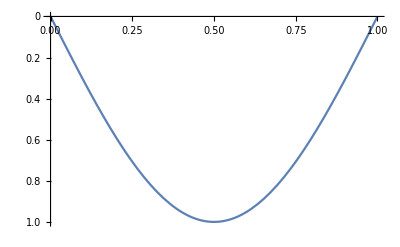

```mathematica
Plot[v[s]/.α->αcr,{s, 0, l}, ScalingFunctions->"Reverse"]
```

# Trave incastro-appoggio elastico

```mathematica
ClearAll["Global`*"]

v[s_] = c1+c2*s+c3*Cos[α*s]+c4*Sin[α*s];

{RR, MM} = CoefficientArrays[
{
v[0] == 0,
v'[0]==0,
v''[l]==0,
-l^3/β*(v'''[l]+α^2*v'[l])==-v[l]
},
{c1,c2,c3,c4}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | α
0 | 0 | -α^2 Cos[l α] | -α^2 Sin[l α]
1 | l-(l^3 α^2)/β | Cos[l α] | Sin[l α])

(0
0
0
0)

```mathematica
Clear[detMM, α, β, l]
detMM[α_] = Det[MM]//Simplify
```

-(α^2 (l α (l^2 α^2-β) Cos[l α]+β Sin[l α]))/β

```mathematica
Solve[β Sin[l α]==0, α]
```

{{α→ConditionalExpression[(2 π C[1])/l, C[1]∈ℤ]},{α→ConditionalExpression[(π+2 π C[1])/l, C[1]∈ℤ]}}

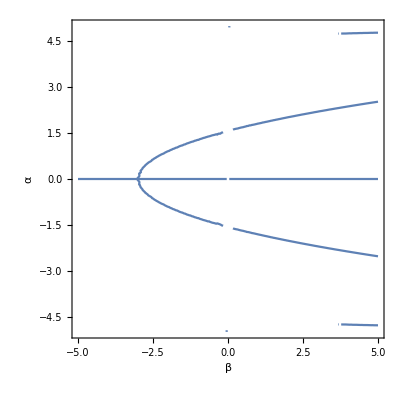

```mathematica
l=1;
ContourPlot[Tan[α l]==(α*l)/β*(β-(α*l)^2), {β, -5, 5}, {α, -5, 5}, FrameLabel->{"β", "α"}]
```

```mathematica
βin = .001;
βfin = 10^5;
step = 1/1000;
nel = (βfin-βin)/step;
l=1;
β0 = Table[β, {β, βin, βfin, step}];
αcr = Table[
α/.FindRoot[
Tan[α*l]==(α*l)/β0[[i]]*(β0[[i]]-(α*l)^2), {α,β0[[i]] }], {i, 1, nel}]
```

$Aborted

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
l=1;
FindRoot[Tan[α*l]==(α*l)/βin*(βin-(α*l)^2), {α,Pi}]
```

FindRoot::nlnum: The function value {-3141.59 l (0.001-9.8696 l^2)+Tan[3.14159 l]} is not a list of numbers with dimensions {1} at {α} = {3.14159}.

FindRoot[Tan[α l]==((α l) (βin-(α l)^2))/βin,{α,π}]

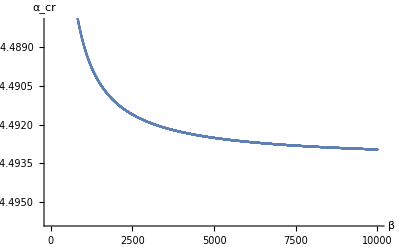

```mathematica
ListPlot[Table[{β0[[i]], αcr[[i]]}, {i, 1, Length[β0]}], AxesLabel->{"β", "α_cr"}]
```

## β -> 0 (k->0)

```mathematica
ClearAll[α, αcr, MMcr, β, l]
β=.001;
l=1;
Plot[detMM[α], {α, 0, 5}, AxesLabel->{"α", "det[M]"}]
```

-Graphics-

```mathematica
αcr = α/.FindRoot[detMM[α]==0, {α, 4}]
Pi//N
```

3.14159

3.14159

```mathematica
MMcr = MM/.α->αcr//Chop;
MatrixForm[MMcr]
Eigensystem[MMcr]
{c1, c2, c3, c4}=Eigenvectors[MMcr][[-2]]
```

(1 | 0 | 1 | 0
0 | 0 | -9.8696 | 0
0 | 0 | 9.8696 | 0
1 | -985.96 | -1. | 0)

{{9.8696,1.,0.,0.},{{0.00112949,-0.0100181,0.0100181,0.999899},{0.707107,0.,0.,0.707107},{0.,0.,0.,1.},{0.,0.,0.,0.}}}

{0.,0.,0.,1.}

```mathematica
Plot[v[s]/.α->αcr,{s, 0, l}, ScalingFunctions->"Reverse"]
```

-Graphics-

## β = kl^3/EJ = 10

```mathematica
ClearAll[α, αcr, MMcr, β, l]
β=10;
l=1;
Plot[detMM[α], {α, 0, 5}, AxesLabel->{"α", "det[M]"}]
```

-Graphics-

```mathematica
αcr = α/.FindRoot[detMM[α]==0, {α, 4}]
Pi//N
```

3.16228

3.14159

```mathematica
MMcr = MM/.α->αcr//Chop;
MatrixForm[MMcr]
Eigensystem[MMcr]
{c1, c2, c3, c4}=Eigenvectors[MMcr][[-1]]
```

(1 | 0 | 1 | 0
0 | 0 | -10. | 0
0 | 0 | 9.99786 | 0.206835
1 | 0 | -0.999786 | -0.0206835)

{{9.97949,0.976466,0.0212256,0.},{{-0.0782707,0.704275,-0.702831,0.0624399},{0.688062,0.165829,-0.0161927,0.706264},{-0.0021573,-0.994795,0.00211151,-0.101848},{0.,1.,0.,0.}}}

{0.,1.,0.,0.}

```mathematica
Plot[v[s]/.α->αcr,{s, 0, l}, ScalingFunctions->"Reverse"]
```

-Graphics-

```mathematica
ClearAll["Global`*"]

v[s_] = c1+c2*s+c3*Cos[α*s]+c4*Sin[α*s];

{RR, MM} = CoefficientArrays[
{
v[0] == 0,
v'[0]==0,
v''[l]==0,
-l^3/β*(v'''[l]+α^2*v'[l])==-v[l]
},
{c1,c2,c3,c4}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | α
0 | 0 | -α^2 Cos[l α] | -α^2 Sin[l α]
1 | l-(l^3 α^2)/β | Cos[l α] | Sin[l α])

(0
0
0
0)

```mathematica
Clear[detMM]
detMM[α_] = Det[MM]//Simplify
```

-(α^2 (l α (l^2 α^2-β) Cos[l α]+β Sin[l α]))/β

```mathematica
β=100000
l=1;
Plot[detMM[α], {α, 0, 5}]
```

100000

-Graphics-

```mathematica
FindRoot[detMM[α]==0,{α,4}]
```

{α→4.49336}

```mathematica
β=.;
α=.;
l=1;
ContourPlot[{detMM[α]==0}, {β, -2, 2},  {α, -5, 5}, Mesh->None, FrameLabel->{"β", "α"}]
```

-Graphics-

## β = kl^3/EJ = 15

```mathematica
ClearAll[α, αcr, MMcr, β, l]
β=15;
l=1;
Plot[detMM[α], {α, 0, 5}, AxesLabel->{"α", "det[M]"}]
```

-Graphics-

```mathematica
αcr = α/.FindRoot[detMM[α]==0, {α, 4}]
Pi//N
```

3.87298

3.14159

```mathematica
MMcr = MM/.α->αcr//Chop;
MatrixForm[MMcr]
Eigensystem[MMcr]
{c1, c2, c3, c4}=Eigenvectors[MMcr][[-1]]
```

(1 | 0 | 1 | 0
0 | 0 | -15. | 0
0 | 0 | 11.1637 | 10.0186
1 | 0 | -0.744246 | -0.667905)

{{10.5944,0.450718+0.861688 ⅈ,0.450718-0.861688 ⅈ,0.},{{-0.0599892+0. ⅈ,0.814902+0. ⅈ,-0.575557+0. ⅈ,0.0327081+0. ⅈ},{0.0313941-0.0546575 ⅈ,-0.993531+0. ⅈ,0.0298535+0.0570742 ⅈ,-0.0368316-0.0584624 ⅈ},{0.0313941+0.0546575 ⅈ,-0.993531+0. ⅈ,0.0298535-0.0570742 ⅈ,-0.0368316+0.0584624 ⅈ},{0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}}

{0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Plot[v[s]/.α->αcr,{s, 0, l}, ScalingFunctions->"Reverse"]
```

-Graphics-

```mathematica
ClearAll["Global`*"]

v[s_] = c1+c2*s+c3*Cos[α*s]+c4*Sin[α*s];

{RR, MM} = CoefficientArrays[
{
v[0] == 0,
v'[0]==0,
v''[l]==0,
-l^3/β*(v'''[l]+α^2*v'[l])==-v[l]
},
{c1,c2,c3,c4}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | 1 | 0 | α
0 | 0 | -α^2 Cos[l α] | -α^2 Sin[l α]
1 | l-(l^3 α^2)/β | Cos[l α] | Sin[l α])

(0
0
0
0)

```mathematica
Clear[detMM]
detMM[α_] = Det[MM]//Simplify
```

-(α^2 (l α (l^2 α^2-β) Cos[l α]+β Sin[l α]))/β

```mathematica
β=100000
l=1;
Plot[detMM[α], {α, 0, 5}]
```

100000

-Graphics-

```mathematica
FindRoot[detMM[α]==0,{α,4}]
```

{α→4.49336}

```mathematica
β=.;
α=.;
l=1;
ContourPlot[{detMM[α]==0}, {β, -2, 2},  {α, -5, 5}, Mesh->None, FrameLabel->{"β", "α"}]
```

-Graphics-

## β = kl^3/EJ = 10000

```mathematica
ClearAll[α, αcr, MMcr, β, l]
β=10000;
l=1;
Plot[detMM[α], {α, 0, 5}, AxesLabel->{"α", "det[M]"}]
```

-Graphics-

```mathematica
αcr = α/.FindRoot[detMM[α]==0, {α, 4}]
Pi//N
```

3.14159

3.14159

```mathematica
MMcr = MM/.α->αcr//Chop;
MatrixForm[MMcr]
Eigensystem[MMcr]
{c1, c2, c3, c4}=Eigenvectors[MMcr][[-2]]
```

(1 | 0 | 1 | 0
0 | 0 | -9.8696 | 0
0 | 0 | 9.8696 | 0
1 | 0.999013 | -1. | 0)

{{9.8696,1.,0.,0.},{{0.0787589,-0.69856,0.69856,-0.133508},{0.707107,0.,0.,0.707107},{0.,0.,0.,1.},{0.,0.,0.,0.}}}

{0.,0.,0.,1.}

```mathematica
Plot[v[s]/.α->αcr,{s, 0, l}, ScalingFunctions->"Reverse"]
```

-Graphics-

```mathematica
β=100000
l=1;
Plot[detMM[α], {α, 0, 5}]
```

100000

-Graphics-

```mathematica
FindRoot[detMM[α]==0,{α,4}]
```

{α→4.49336}

```mathematica
β=.;
α=.;
l=1;
ContourPlot[{detMM[α]==0}, {β, -2, 2},  {α, -5, 5}, Mesh->None, FrameLabel->{"β", "α"}]
```

-Graphics-